```mathematica
data=Import["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/15n-0n-on-25n_0420-0624.csv","Numeric"->True];
data=Delete[data, 1];
{baseline, gnn}=GatherBy[data,First];
baseline=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@baseline);
gnn=Drop[#,{2,3}]&/@(Drop[#,{1,6}]&/@gnn);
```

```mathematica
(*{stime|walltime|proctime}*)
baselineWall=Part[#,2]&/@baseline;
gnnWall=Part[#,2]&/@gnn;
size=Min[Length[baselineWall],Length[gnnWall]]
baselineWallnormal=baselineWall[[1;;size]];
(*baselineWalltransferS=baselineWall[[101;;size]];
baselineWalltransferM=baselineWall[[201;;300]];
baselineWalltransferL=baselineWall[[301;;transferLsize]];*)
gnnWallnormal=gnnWall[[1;;size]];
(*gnnWalltransferS=gnnWall[[101;;size]];
gnnWalltransferM=gnnWall[[201;;300]];
gnnWalltransferL=gnnWall[[301;;transferLsize]];*)
```

135

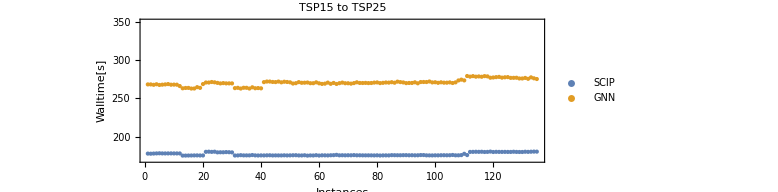

```mathematica
p1=Show[
ListPlot[{baselineWallnormal,gnnWallnormal},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.8}]
],
PlotRange->{Automatic,{170, 350}},
PlotLabel->Style["TSP15 to TSP25"],
AxesOrigin->{0,0},
AspectRatio->1/3,
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/Plots/15-25.png",p1];
```

```mathematica
Mean[baselineWallnormal-gnnWallnormal]/Mean[baselineWallnormal]*100
```

-53.061

```mathematica
p1=Show[
ListPlot[{baselineWalltransferS,gnnWalltransferS},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.9}]
],
PlotRange->{Automatic,Automatic},
PlotLabel->Style["TSP15 to TSP25"],
AxesOrigin->{0,0},
ImageSize->Large
]
Export["/Users/pbb/University/UM/Junior/2022WN/EECS545/Project/EECS545-Project/results/Plots/15-25.png",p1];
```

```mathematica
(*Show[
ListPlot[{baselineWalltransferM,gnnWalltransferM},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.9}]
],
PlotRange->{Automatic,{0,0.6}},
PlotLabel->Style["TSP15 to TSP25"],
AxesOrigin->{0,0},
ImageSize->Large
]*)
```

```mathematica
(*Show[
ListPlot[{baselineWalltransferL,gnnWalltransferL},
Frame->True, FrameLabel->{"Instances","Walltime[s]"},
 PlotStyle->PointSize[Medium], 
PlotLegends->Placed[LineLegend[{"SCIP","GNN"}],{0.9,0.9}]
],
PlotRange->{Automatic,{300,500}},
PlotLabel->Style["TSP15 to TSP25"],
AxesOrigin->{0,0},
ImageSize->Large
]*)
```